```mathematica
(* Numerical Specification of the Landau-Zener Problem *)
```

```mathematica
Clear[H,T];
H[s_,{Δ_}]:=({{s, Δ}, {Δ, -s}});

Ω[index_,{Δ_}]:=Module[{s,ϕ,ϵ},
s=sValues[[index]];

{ϵ,ϕ}=Eigensystem[H[s,{Δ}]];
{ϵ,ϕ}={ϵ[[#]],ϕ[[#]]}&@Ordering[ϵ];

Table[
KroneckerDelta[i,k]KroneckerDelta[j,l](ϵ[[i]]-ϵ[[j]])
,
{i,1,2},{j,1,2},{k,1,2},{l,1,2}]
];
M[{index_,badIndices_},{Δ_}]:=Module[{sp1,sm1,ϕp1,ϕm1,ϵp1,ϵm1,Δt,bkt},
If[index==1 ∨index ≥Length[sValues]∨MemberQ[badIndices,index],
Table[0,
{i,1,2},{j,1,2},{k,1,2},{l,1,2}],

sp1=sValues[[index+1]];
sm1=sValues[[index-1]];

{ϵp1,ϕp1}=Eigensystem[H[sp1,{Δ}]];
{ϵp1,ϕp1}={ϵp1[[#]],ϕp1[[#]]}&@Ordering[ϵp1];

{ϵm1,ϕm1}=Eigensystem[H[sm1,{Δ}]];
{ϵm1,ϕm1}={ϵm1[[#]],ϕm1[[#]]}&@Ordering[ϵm1];

Δt=tValues[[index+1]]-tValues[[index]];

bkt[n_,m_]:=1/(4Δt)(ϕp1[[n]]+ϕm1[[n]]).(ϕp1[[m]]-ϕm1[[m]]);

Table[KroneckerDelta[i,k]bkt[l,j]+KroneckerDelta[j,l]bkt[k,i],
{i,1,2},{j,1,2},{k,1,2},{l,1,2}]
]
];
Λ[{index_,badIndices_},{Δ_}]:= Ω[index,{Δ}]+ M[{index,badIndices},{Δ}];
Vectorize[ρ_]:=Module[{ρVector},
ρVector[Ι_]:=Module[{i,j},
{i,j} =(#+1)&/@QuotientRemainder[Ι-1,2];
ρ[[i,j]]
];

Table[ρVector[Ι],{Ι,1,4}]
];

Compactify[Λ_]:=Module[{ΛMatrix},
ΛMatrix[Ι_,J_]:=Module[{i,j,k,l},
{i,j} =(#+1)&/@QuotientRemainder[Ι-1,2];
{k,l} =(#+1)&/@QuotientRemainder[J-1,2];
Λ[[i,j,k,l]]];

Table[ΛMatrix[Ι,J],{Ι,1,4},{J,1,4}]
];
```

```mathematica
(* Tools for Integration of the Quantum Liouville Equation*)
```

```mathematica
TRUpdate[ρn_,{Λn_,Λn1_},dtn_]:=Module[{Ι,B1,B2},
Ι=IdentityMatrix[Length[ρn]];
B1=Inverse[Ι-(dtn/2)Λn1];
B2=Ι+(dtn/2)Λn;
B1.(B2.ρn)
];
IntegrateODE[ρ0_,L_]:=Module[{ρ},
ρ=Table[ρ0,{t,1,Length[L]}];
For[t=1,t<Length[sValues],t++,

ρ[[t+1]]=TRUpdate[ρ[[t]],{L[[t]],L[[t+1]]},tValues[[t+1]]-tValues[[t]]]

(*If[Mod[index,Round[Length[L]/10]]== 0, Print[index]];*)
];
ρ
];
GenerateSValues[START_,END_,MaxSSTEP_,SCALE_]:=Module[
{sValues,ϵ,gap,SSTEP},
sValues={START};
i=1;
While[sValues[[i]]<END,
ϵ=Sort[Eigenvalues[H[sValues[[i]],{Δ}]]];
gap=ϵ[[2]]-ϵ[[1]];
SSTEP=Min[MaxSSTEP,END-sValues[[i]],SCALE * gap];
sValues=Catenate[{sValues,{sValues[[i]]+SSTEP}}];
i=i+1;
];
sValues
];
GenerateSValuesv2[START_,END_,SSTEP_,{ΔLOCATION_,Δ_,WINDOWSIZE_,NUMSAMPLES_}]:=Module[{Startlist,Middlelist,Endlist,sValues,badIndices},
Middlelist=Range[Max[ΔLOCATION-(WINDOWSIZE Δ)/2+(WINDOWSIZE Δ)/NUMSAMPLES,START],Min[ΔLOCATION+(WINDOWSIZE Δ)/2-(WINDOWSIZE Δ)/NUMSAMPLES,END],(WINDOWSIZE Δ)/NUMSAMPLES];

If[ΔLOCATION-(WINDOWSIZE Δ)/2>START,

Startlist=Range[START,ΔLOCATION-(WINDOWSIZE Δ)/2,SSTEP];,
Startlist={};
];

If[ΔLOCATION+(WINDOWSIZE Δ)/2<END,
Endlist=Range[ΔLOCATION+(WINDOWSIZE Δ)/2,END,SSTEP];,
Endlist={};
];
badIndices={Length[Startlist],Length[Startlist]+Length[Middlelist]+1};
sValues=Catenate[{Startlist,Middlelist,Endlist}];
{sValues,badIndices}
];
```

```mathematica
{sValues,badIndices}=GenerateSValuesv2[-1,1,.01,{0,.01,10,10000}];//AbsoluteTiming
Length[sValues]
```

{0.00071,Null}

10191

```mathematica
badIndices
```

{96,10098}

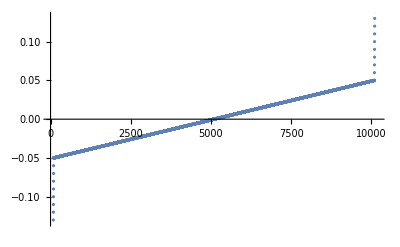

```mathematica
ListPlot[sValues]
```

```mathematica
sValues=GenerateSValues[-1,1,.01,.0005];//AbsoluteTiming
Length[sValues]
```

{0.85886,Null}

10598

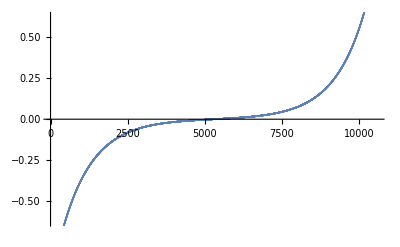

```mathematica
ListPlot[sValues]
```

```mathematica
GenerateSValues[-2,2,.01,.001];
```

```mathematica
(* Here is how one would specify/solve the Landau-Zener Problem *)
```

```mathematica
Δ=.01;
T=1 10^-1;
α=1/T;
{sValues,badIndices}=GenerateSValuesv2[-3,3,.01,{0,Δ,20,40000}];
tValues=(T#)&/@sValues;
ρ0={1,0,0,0};
L=Compactify[Λ[{#,badIndices},{Δ}]]&/@Range[1,Length[sValues]];//AbsoluteTiming
ρ=IntegrateODE[ρ0,L];//AbsoluteTiming
ρ[[-2,1]]
```

{42.98316,Null}

{3.03969,Null}

0.0000609526

0.0000628299

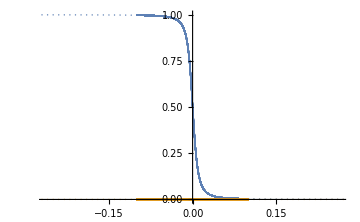

```mathematica
Γ[{α_,Δ_}]:=Δ^2/Abs[α];
P[{α_,Δ_}]:=1-ⅇ^(-2π Γ[{α,Δ}]);
PTheory=Table[P[{α,Δ}],{i,1,Length[sValues]}];
P[{α,Δ}]
ListPlot[{Transpose[{sValues,ρ[[;;,1]]}],Transpose[{sValues,PTheory[[;;]]}]},PlotRange->{0,1},ImageSize->Medium]
```

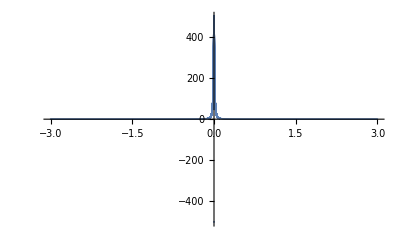

```mathematica
ListPlot[Transpose[{sValues,L[[;;,1,3]]}],PlotRange->All]
```

```mathematica
Δ=.1;
T=1 10^-1;
α=1/T;
sValues=GenerateSValues[-1,1,.01,.001];
badIndices={};
tValues=(T#)&/@sValues;
ρ0={1,0,0,0};
L=Compactify[Λ[{#,badIndices},{Δ}]]&/@Range[1,Length[sValues]];//AbsoluteTiming
ρ=IntegrateODE[ρ0,L];//AbsoluteTiming
ρ[[-2,1]]
```

{2.93808,Null}

{0.19434,Null}

0.010572

0.00626349

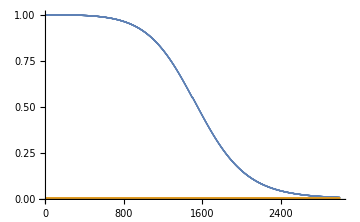

```mathematica
Γ[{α_,Δ_}]:=Δ^2/Abs[α];
P[{α_,Δ_}]:=1-ⅇ^(-2π Γ[{α,Δ}]);
PTheory=Table[P[{α,Δ}],{i,1,Length[sValues]}];
P[{α,Δ}]
ListPlot[{ρ[[;;,1]],PTheory[[;;]]},PlotRange->{0,1},ImageSize->Medium]
```

```mathematica
Length[ρ[[;;,1]]]
```

20001

```mathematica
Length[PTheory]
```

20001

```mathematica
(* Tests of Compactify[] *)
```

```mathematica
ρ=Table[RandomReal[],{i,1,2},{j,1,2}];
L=Table[RandomReal[],{i,1,2},{j,1,2},{k,1,2},{l,1,2}];
```

```mathematica
Compactify[L].Vectorize[ρ]
```

{0.562856,0.999706,1.3155,1.1603}

```mathematica
Vectorize[Table[∑_(k=1)^2 ∑_(l=1)^2 L[[i,j,k,l]]ρ[[k,l]],{i,1,2},{j,1,2}]]
```

{0.562856,0.999706,1.3155,1.1603}

```mathematica
(* Tests of IntegrateODE[] *)
```

```mathematica
T=10;
sValues=Range[0,1,.01];
tValues=(T#)&/@sValues;
λ=-3;
ρ0={1,1};
L={{λ,0},{0,λ}}&/@Range[1,Length[sValues]];
(*ρ=IntegrateODE[ρ0,L];*)
```

```mathematica
ρ=Table[ρ0,{t,1,Length[L]}];
For[t=1,t<Length[sValues],t++,

ρ[[t+1]]=TRUpdate[ρ[[t]],{L[[t]],L[[t+1]]},tValues[[t+1]]-tValues[[t]]]

(*If[Mod[index,Round[Length[L]/10]]== 0, Print[index]];*)
]
```

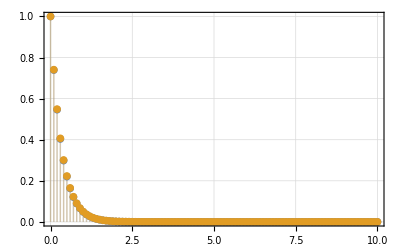

```mathematica
ListPlot[{Transpose[{tValues,ρ[[;;,1]]}],Transpose[{tValues,ⅇ^(λ#)&/@tValues}]},Filling->Axis,PlotTheme->"Detailed",PlotRange->All]
```

```mathematica
ρ=Table[ρ0,{t,1,Length[L]}];
```

```mathematica
t=1;
ρ[[t+1]]=TRUpdate[ρ[[t]],{L[[t]],L[[t+1]]},tValues[[t+1]]-tValues[[t]]]
```

{-0.666667,-0.666667}

```mathematica
t=2;
ρ[[t+1]]=TRUpdate[ρ[[t]],{L[[t]],L[[t+1]]},tValues[[t+1]]-tValues[[t]]]
```

{0.444444,0.444444}

```mathematica
t=3;
ρ[[t+1]]=TRUpdate[ρ[[t]],{L[[t]],L[[t+1]]},tValues[[t+1]]-tValues[[t]]]
```

{-0.296296,-0.296296}